```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
nContestants = 1000;
lCar=RandomVariate[DiscreteUniformDistribution[{1,4}],{nContestants}];
lAvailable=Drop[Range@4,{#}]&/@lCar;
lPenaltyIndex = RandomVariate[DiscreteUniformDistribution[{1,3}],{nContestants}];
lPenalty = Table[Extract[lAvailable[[i]],lPenaltyIndex[[i]]],{i,1,nContestants ,1}];
```

```mathematica
fCompete[doChange_Integer,aReward_,aCost_]:= Module[{aCar = RandomVariate[DiscreteUniformDistribution[{1,4}],{1}][[1]],lAvailable,aPenaltyIndex,aPenalty,lNonEvents,aInitChoice,lRemaining,aOpen,aFinal,aOutcome},lAvailable=Drop[Range@4,{aCar}];aPenaltyIndex = RandomVariate[DiscreteUniformDistribution[{1,3}],{1}][[1]];
aPenalty=Extract[lAvailable,{aPenaltyIndex }];
lNonEvents=Delete[Range@4,{{aCar},{aPenalty}}];
aInitChoice = RandomVariate[DiscreteUniformDistribution[{1,4}],{1}][[1]];
lRemaining = Drop[Range@4,{aInitChoice}];
If[aInitChoice==lNonEvents[[1]],aOpen= lNonEvents[[2]],If[aInitChoice==lNonEvents[[2]],aOpen= lNonEvents[[1]],aOpen = lNonEvents[[RandomInteger[{1,2}]]]]];
lRemaining = DeleteCases[lRemaining,aOpen]; If[doChange==1,aFinal = lRemaining[[RandomInteger[{1,2}]]],aFinal=aInitChoice];
If[aFinal==aCar,aOutcome= aReward,If[aFinal==aPenalty,aOutcome=-aCost,aOutcome=0]];aOutcome
]
```

```mathematica
N@StandardDeviation@Table[fCompete[0,1000,1000],{10000}]
```

708.13

```mathematica
N@StandardDeviation@Table[fCompete[1,1000,1000],{10000}]
```

869.499

```mathematica
N@Mean@Table[fCompete[0,1000,1000],{10000}]
```

7.6

```mathematica
N@Mean@Table[fCompete[1,1000,1000],{10000}]
```

-6.8

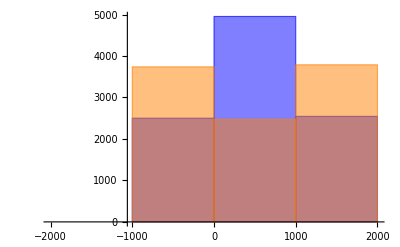

```mathematica
Histogram[{Table[fCompete[0,1000,1000],{10000}],Table[fCompete[1,1000,1000],{10000}]},ChartStyle->{Blue,Orange}]
```